# The simulation when the cylinder rolls around on the ground

## Define equations

```mathematica
eq={
m2(x0''[t]+R(θ''[t]Cos[θ[t]]-θ'[t]^2 Sin[θ[t]]))==-f2[t] Cos[θ[t]]+Fn2[t] Sin[θ[t]],
m2 R(-θ''[t] Sin[θ[t]]-θ'[t]^2 Cos[θ[t]])==f2[t] Sin[θ[t]]+Fn2[t] Cos[θ[t]]-m2 g,
f2[t]-f1[t]==x0''[t]/R^2 i,
f1[t]+f2[t] Cos[θ[t]]-Fn2[t] Sin[θ[t]]==m1 x0''[t]
}
```

{m2 (x0''[t]+R (-Sin[θ[t]] θ'[t]^2+Cos[θ[t]] θ''[t]))==-Cos[θ[t]] f2[t]+Fn2[t] Sin[θ[t]],m2 R (-Cos[θ[t]] θ'[t]^2-Sin[θ[t]] θ''[t])==-g m2+Cos[θ[t]] Fn2[t]+f2[t] Sin[θ[t]],-f1[t]+f2[t]==(i x0''[t])/R^2,f1[t]+Cos[θ[t]] f2[t]-Fn2[t] Sin[θ[t]]==m1 x0''[t]}

## Define initial conditions

```mathematica
initial={x0[0]==0,x0'[0]==0,θ[0]==0,θ'[0]==0}
```

{x0[0]==0,x0'[0]==0,θ[0]==0,θ'[0]==0}

## Define parameters

```mathematica
params={m1->4,m2->1,g->9.8,i->1,R->1}
```

{m1→4,m2→1,g→9.8,i→1,R→1}

## Control equation

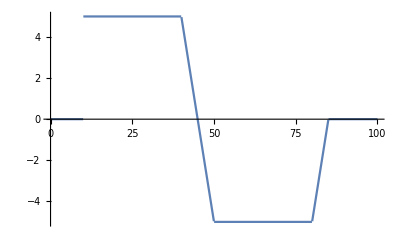

f2[t]==0.1 (-(Piecewise[{{0, t<10}, {5, t<40}, {45-t, t<50}, {-5, t<80}, {-85+t, t<85}, {0, True}}])+x0[t])+10 θ[t]+0.5 x0'[t]+θ'[t]

```mathematica
goal[t_]:=Piecewise[{{0,t<10},{5,t<40},{5-(t-40),t<50}, {-5,t<80},{-5+(t-80),t<85}},0];
(*goal2[t_]:=InterpolatingFunction*)
Plot[{goal[t]},{t,0,100}]
ceq=f2[t]==10θ[t]+θ'[t]+.1(x0[t]-goal[t])+.5 x0'[t]
```

## Solve ODE

```mathematica
sol=NDSolveValue[{eq,initial,ceq}/.params,{x0,θ,f1},{t,0,120},MaxSteps->Infinity]
```

NDSolveValue::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

{InterpolatingFunction[{{0., 120.}}, <>],InterpolatingFunction[{{0., 120.}}, <>],InterpolatingFunction[{{0., 120.}}, <>]}

```mathematica
Dynamic@Plot[Evaluate[#[t]&/@sol],{t,0,40},PlotRange->All,PlotLegends->Automatic]
```

## Visualize results

```mathematica
<<"visualization.m"
```

```mathematica
Manipulate[getBB8[sol[[1]][t],sol[[2]][t]]/.t->tt,{tt,0,120}]
```